## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; r1 = 40; mu = 0.3;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.32763+1.42869×10^-9 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.478123

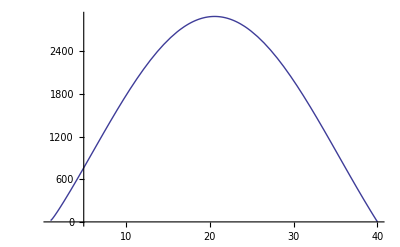

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25+0.000001*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 +ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,200}];
t2r=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,200}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25+0.000001*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 - ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,100};
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{1.66667,1.42869×10^-9},{1.65,1.34167×10^-9},{1.63333,1.2575×10^-9},{1.61667,1.1762×10^-9},{1.6,1.09778×10^-9},{1.58333,1.02225×10^-9},{1.56667,9.49631×10^-10},{1.55,8.7994×10^-10},{1.53333,8.13131×10^-10},{1.51667,7.49237×10^-10},{1.5,6.88266×10^-10},{1.48333,6.30198×10^-10},{1.46667,5.75043×10^-10},{1.45,5.22777×10^-10},{1.43333,4.73396×10^-10},{1.41667,4.26934×10^-10},{1.4,3.83196×10^-10},{1.38333,3.42337×10^-10},{1.36667,3.0424×10^-10},{1.35,2.68909×10^-10},{1.33333,2.36226×10^-10},{1.31667,2.06193×10^-10},{1.3,1.7872×10^-10},{1.28333,1.53739×10^-10},{1.26667,1.31139×10^-10},{1.25,1.11922×10^-10},{1.23333,9.26089×10^-11},{1.21667,7.63554×10^-11},{1.2,7.9×10^-11},{1.18333,4.86863×10^-11},{1.16667,3.93475×10^-11},{1.15,2.50177×10^-11},{1.13333,-1.95944×10^-11},{1.11667,7.68637×10^-13},{1.1,-1.85077×10^-11},{1.08333,-3.40498×10^-11},{1.06667,-5.92049×10^-11},{1.05,-9.31948×10^-11},{1.03333,-1.39745×10^-10},{1.01667,-2.02021×10^-10},{1.,-2.85555×10^-10},{0.983333,-3.98865×10^-10},{0.966667,-5.47106×10^-10},{0.95,-7.40254×10^-10},{0.933333,-9.88848×10^-10},{0.916667,-1.30593×10^-9},{0.9,-1.70552×10^-9},{0.883333,-2.20196×10^-9},{0.866667,-2.82312×10^-9},{0.85,-3.58189×10^-9},{0.833333,-4.49905×10^-9},{0.816667,-5.62583×10^-9},{0.8,-6.97173×10^-9},{0.783333,-8.581×10^-9},{0.766667,-1.04949×10^-8},{0.75,-1.27593×10^-8},{0.733333,-1.54266×10^-8},{0.716667,-1.85552×10^-8},{0.7,-2.22104×10^-8},{0.683333,-2.64654×10^-8},{0.666667,-3.14026×10^-8},{0.65,-3.71106×10^-8},{0.633333,-4.36927×10^-8},{0.616667,-5.12622×10^-8},{0.6,-5.99434×10^-8},{0.583333,-6.98756×10^-8},{0.566667,-8.12133×10^-8},{0.55,-9.41308×10^-8},{0.533333,-1.08813×10^-7},{0.516667,-1.25472×10^-7},{0.5,-1.44342×10^-7},{0.483333,-1.65672×10^-7},{0.466667,-1.89751×10^-7},{0.45,-2.1689×10^-7},{0.433333,-2.47432×10^-7},{0.416667,-2.81754×10^-7},{0.4,-3.20276×10^-7},{0.383333,-3.63451×10^-7},{0.366667,-4.11793×10^-7},{0.35,-4.6585×10^-7},{0.333333,-5.26233×10^-7},{0.316667,-5.9361×10^-7},{0.3,-6.68715×10^-7},{0.283333,-7.52354×10^-7},{0.266667,-8.45407×10^-7},{0.25,-9.48843×10^-7},{0.233333,-1.06372×10^-6},{0.216667,-1.1912×10^-6},{0.2,-1.33255×10^-6},{0.183333,-1.48915×10^-6},{0.166667,-1.66253×10^-6},{0.15,-1.85435×10^-6},{0.133333,-2.06641×10^-6},{0.116667,-2.30069×10^-6},{0.1,-2.55937×10^-6},{0.0833333,-2.84478×10^-6},{0.0666667,-3.15951×10^-6},{0.05,-3.50637×10^-6},{0.0333333,-3.8884×10^-6},{0.0166667,-4.30893×10^-6},{0.,-4.77161×10^-6}}

```mathematica
(*The imaginary part vs the radius*)
```

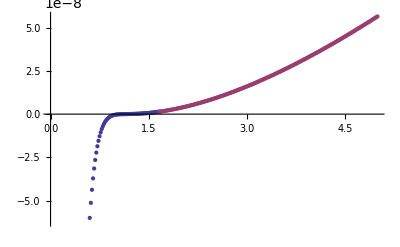

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

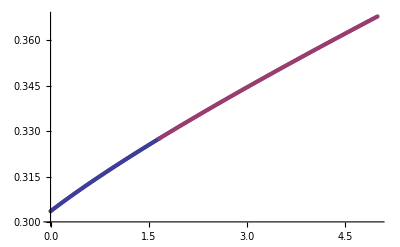

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.3/r=40/Q=0.999/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.3/r=40/Q=0.999/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/q/mu0.3/r=40/Q=0.999/R.dat

/home/h/skoli/pt/rnef/mathematica/q/mu0.3/r=40/Q=0.999/I.dat